# A toy function parsing expression order from LATEX input

## The function

```mathematica
detectOrderOfTeXExpression[string_,form_:TeXForm]:=Module[
(*Declare our local variables*)
{expression,monomials,variables,exponents,periods},
(*Convert our string to an expression; LaTeX is the default, can also accept MathML et al, as listed at https://reference.wolfram.com/language/tutorial/TextualInputAndOutput.html#12368 *)
expression=ToExpression[string,form];
(*Extract variables by deleting everything that isn't a Symbol, recursing infinitely down the expression tree*)
variables=Union@Cases[expression,Except[__Symbol?(Context@#==="System`"&),_Symbol],{0,∞},Heads->True];
monomials=MonomialList[expression];
(*Extract the largest exponent to which every detected variable appears*)
exponents=AssociationMap[Function[{variable},
DeleteDuplicates@Flatten[{
(*Extract cases where the variable is raised to an exponent*)
Cases[FullForm[#],Power[variable,exp_]:>exp,All]&/@monomials,
(*Extract cases where the variable appears linearly, filtering the monomials for those where the variable appears with an exponent*)
Cases[FullForm[#],variable:>1,All]&/@(DeleteCases[monomials,Power[variable,_],Infinity])
}]]
,variables];
(*Determine the periods of the function in each variable detected*)
periods=FunctionPeriod[expression,#]&/@variables;
(*Return an association examining the values constructed above*)
<|
"degree"->  AssociationMap[<|
"Linear"->MemberQ[exponents[#],1],
"Quadratic"-> MemberQ[exponents[#],2],
"Cubic"-> MemberQ[exponents[#],3],
"Higher Order Polynomial"->AnyTrue[exponents[#],#>3===True&],
(*Note that this returns true for any non-numeric exponents, including Complex*)
"Exponential"->AnyTrue[exponents[#],Not@NumericQ@#===True&]
|>&,variables],
(*A field for expression-wide characeteristics which are not the degree*)
"character"-> <|
"Has Constant Term"->Length@Cases[MonomialList[expression],_?NumericQ]>0,
"Complex"->(ComplexExpand@Im@expression≠0)===True,
"Periodic"->AnyTrue[periods,#≠0&]
|>,
(*Pass along the original data we derived these from for convenience of debugging*)
"data"-> <|
"expression"->expression,
"monomials"->monomials,
"variables"->variables,
"exponents"->exponents,
"periods"->periods
|>
|>
]
```

```mathematica
detectOrderOfTeXExpression["3^{(x-2)}+4"]
```

<|degree→<|x→<|Linear→True,Quadratic→False,Cubic→False,Higher Order Polynomial→False,Exponential→False|>|>,character→<|Has Constant Term→False,Complex→False,Periodic→False|>,data→<|expression→4+3^(-2+x),monomials→{4+3^(-2+x)},variables→{x},exponents→<|x→{1}|>,periods→{0}|>|>

## Testing our function with a few examples of LATEX input

```mathematica
prettyPrint[analysis_]:=Module[
{exprDesc,degreeDesc,characterDesc},
exprDesc=TraditionalForm[analysis["data"]["expression"]];
degreeDesc={
StringRiffle[PositionIndex[analysis["degree"][#]][True]," & "],
"in",
#}&/@analysis["data"]["variables"];
characterDesc=Lookup[PositionIndex[analysis["character"]],True,Null];
{
exprDesc,
StringRiffle[StringRiffle[#," "]&/@degreeDesc,"\n"],
If[characterDesc===Null,"",
StringRiffle[characterDesc, " & "]] 
}
]
```

```mathematica
Join[
{{"Expression","Degree","Character"}},
prettyPrint[detectOrderOfTeXExpression[#]]&/@{
"x",
"x^2",
"(x+1)(x+1)",
"(x+1)(x-1)",
"e^x",
"e^(x^2)",
(*Note that TeX expressions need to be properly escaped*)
"\\sin(x)",
"(\\sin(x))^2"
}
]//TextGrid[#,Frame->All]&
```

Expression | Degree | Character
x | Linear in x | 
x^2 | Quadratic in x | 
(x+1)^2 | Linear & Quadratic in x | Has Constant Term
(x-1) (x+1) | Quadratic in x | Has Constant Term
e^x | Exponential in e
Linear in x | 
e^(x^2) | Exponential in e
Quadratic in x | 
sin(x) | Linear in x | Periodic
sin^2(x) | Linear in x | Periodic

## Improving the extraction of exponents

In our earlier functions, because we are only looking at variables, we can easily miss exponentiation involving variables if the base is a constant, as in 3^x.  We can improve on this by recognizing that we can treat expressions as trees.  Let’s consider 4+3^(x-2)…

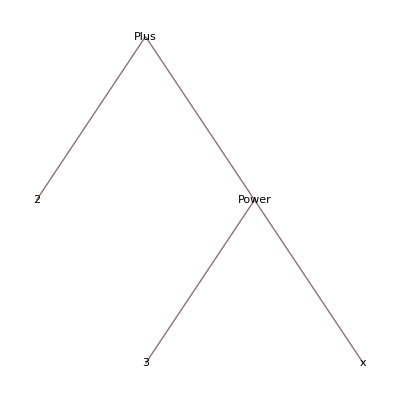

```mathematica
TreeForm[4+3^x-2]
```

We’re looking to look at the expression at each level and ascertain whether the base or the exponent (i.e. either argument to `Power`).

```mathematica
Level[4+3^x-2,{0}]
Level[4+3^x-2,{1}]
Level[4+3^x-2,{2}]
```

{2+3^x}

{2,3^x}

{3,x}

We can do this using Cases, which can be targeted to a particular level using the levelspec parameter.

```mathematica
Cases[4+3^x-2,Power[_,_],{0}]
Cases[4+3^x-2,Power[_,_],{1}]
Cases[4+3^x-2,Power[_,_],{2}]
```

{}

{3^x}

{}

This matches since we’re using patterns to match any expression involving two arguments to `Power`.  Noting that a term may appear with a variable but no explicit power (e.g. x is not represented as `Power[x,1]` internally), we can create a simple function to extract exponents from an expression containing a variable as follows…

```mathematica
extractExponents[expression_,variable_]:=Module[
{explicitPowers},
With[
{
coeffs=CoefficientList[expression,variable][[2;;]], (*For convenience, a coefficient list dropping the constant (zeroth degree) term*)
expandedExpression=Expand[expression] (*Expanding to capture degeree in expressions like (1+x)^2*)
},
explicitPowers=Merge[{ (*Merge two associations, creating a list from values with shared keys*)
Cases[expandedExpression,Power[base_,power_]:><|base->power|>,{0,Infinity}],(*Looking for cases at all levels in expression where a base is raise to a power and returning the map between those*)
If[Length[coeffs]≥1,(*If we have a coefficient list*)
<|variable->Position[coeffs,_?Positive]|>,(*Return a mapping of the variable to the indices of all the positive coefficients (1 for linear, 2 for quadratic, etc. ) Note that this works because we truncated the zeroth degree iwhen defining coeffs*)
<||>]
},
DeleteDuplicates@*Flatten (*Here we remove any duplicates and nested lists introduced by merging values for shared keys.*)
];
KeySelect[ (*Now we're going to select from this association (which contains bases mapped to exponents)*)
explicitPowers,
!FreeQ[#,variable](* Looking for cases where either the key (base) contains the variable*)
||!FreeQ[explicitPowers[#],variable]&(*Or cases where the value (exponent) contains the variable*)
] (*And returning the resulting, filtered association*)
]
];
```

### Testing our function for extracting exponents

```mathematica
extractExponents[4+3^(x-2),x]
```

<|3→{-2+x}|>

```mathematica
ToExpression[#,TeXForm]&/@{
"x",
"x^2",
"(x+1)(x+1)",
"(x+1)(x-1)",
"e^x",
"e^(x^2)",
"\\sin(x)",
"(\\sin(x))^2"
}
```

{x,x^2,(1+x)^2,(-1+x) (1+x),e^x,e^(x^2),Sin[x],Sin[x]^2}

```mathematica
extractExponents[#,x]&/@%
```

{<|x→{1}|>,<|x→{2}|>,<|x→{2,1}|>,<|x→{2}|>,<|e→{x}|>,<|x→{2},e→{x^2}|>,<||>,<|Sin[x]→{2}|>}

Note that this does not yet work when x is an argument of a function itself (as in the Sin) cases.